1.70184

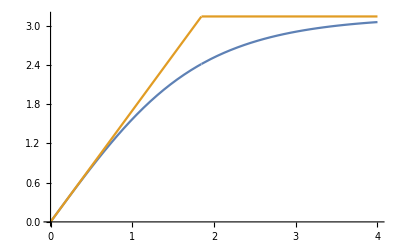

```mathematica
w=1.;R=1.;L=4R;
μ=1.; ϕ0=-2π/2;
dr0 = D[θsk[r],r]/.r->0
Clear[θsk]
Clear[θsk2]
θsk[r_]:=2ArcTan[Sinh[r/w]/Sinh[R/w]](* single skyrmion profile *)
θsk2[r_]:=π Clip[dr0(r/R)/π,{10^-12,1-10^-12}](* single skyrmion profile *)
Plot[{θsk[r],θsk2[r]},{r,0,L},PlotRange->Full]
HueVlad[spec_]:=Hue[{0.5+spec[[1]],spec[[2]],spec[[3]]}]
m[θ_,ϕ_]:={Cos[ϕ]Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]}/2
M[θ_,ϕ_,csq_]:=m[θ,-ϕ]+csq(m[θ,ϕ]-m[θ,-ϕ])
Φ[ϕ_]:=Clip[Mod[μ ϕ + ϕ0,2π]-π,{-π+10^-12,π-10^-12}]
```

```mathematica
xs=Table[x,{x,-L+10^-8,L-10^-8,L/10}];
ys=xs;
listCart=Flatten[Table[{x0={x,y,0}-0.(mm=m[θsk[Norm[{x,y}]],Φ[ArcTan[x,y]]]),x0+mm,{(ArcTan[mm[[1]],mm[[2]]]+π)/(2π),(mm[[3]]+1)/2,-mm[[3]]+1}},{x,xs},{y,ys}],1];
listSp=Flatten[Table[{x0=FromSphericalCoordinates[{1,θsk[Norm[{x,y}]],ArcTan[x,y]}],x0+(mm=m[θsk[Norm[{x,y}]],Φ[ArcTan[x,y]]]),{(ArcTan[mm[[1]],mm[[2]]]+π)/(2π),(mm[[3]]+1)/2,-mm[[3]]+1}},{x,xs},{y,ys}],1];

skCart=Graphics3D[{HueVlad[#[[3]]],Arrowheads[.03],Arrow[Tube[#[[;;2]]]]}&/@listCart,ViewPoint->Top,Boxed->False];
skSph=Graphics3D[{HueVlad[#[[3]]],Arrowheads[.05],Arrow[Tube[#[[;;2]]]]}&/@listSp];
skSph=Show[Graphics3D[{Opacity[0.1],Sphere[]}],skSph,ViewPoint->Top,Boxed->False];
listCart=Flatten[Table[{x0={x,y,0}-0.(mm=m[θsk[Norm[{x,y}]],-Φ[ArcTan[x,y]]]),x0+mm,{(ArcTan[mm[[1]],mm[[2]]]+π)/(2π),(mm[[3]]+1)/2,-mm[[3]]+1}},{x,xs},{y,ys}],1];
listSp=Flatten[Table[{x0=FromSphericalCoordinates[{1,θsk[Norm[{x,y}]],-ArcTan[x,y]}],x0+(mm=m[θsk[Norm[{x,y}]],Φ[ArcTan[x,y]]]),{(ArcTan[mm[[1]],mm[[2]]]+π)/(2π),(mm[[3]]+1)/2,-mm[[3]]+1}},{x,xs},{y,ys}],1];

askCart=Graphics3D[{HueVlad[#[[3]]],Arrowheads[.03],Arrow[Tube[#[[;;2]]]]}&/@listCart,ViewPoint->Top,Boxed->False];
askSph=Graphics3D[{HueVlad[#[[3]]],Arrowheads[.05],Arrow[Tube[#[[;;2]]]]}&/@listSp];
askSph=Show[Graphics3D[{Opacity[0.1],Sphere[]}],askSph,ViewPoint->Top,Boxed->False];
im2=GraphicsGrid[{{skCart,askCart},{skSph,askSph}}]
```

-Graphics-

{ConditionalExpression[π-1/2 ArcCos[-Cot[θ]^2], π/4<θ<(3 π)/4],ConditionalExpression[-1/2 ArcCos[-Cot[θ]^2], π/4<θ<(3 π)/4],ConditionalExpression[1/2 ArcCos[-Cot[θ]^2], π/4<θ<(3 π)/4],ConditionalExpression[1/4 (-3 π+2 ArcSin[Cot[θ]^2]), π/4<θ<(3 π)/4]}

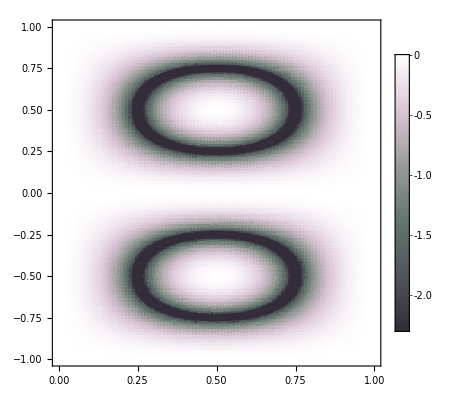

```mathematica
(* orthogonality between skyrmion and anti-skyrmion *)
clip=Log[10^-1];
$Assumptions=0<θ<=π&&-π<ϕ<=π;
solutions =ϕ/. FullSimplify[Solve[m[θ,ϕ].m[θ,-ϕ]==0,ϕ]]
DensityPlot[Log[Abs[4m[θ π,ϕ π].m[θ π,-ϕ π]]],{θ,10^-12,1},{ϕ,-1+10^-12,1},PlotLegends->Automatic,PlotPoints->100,PlotTheme->"Scientific",ColorFunction->(ColorData["PigeonTones"][Rescale[#,{clip,0}]]&),ColorFunctionScaling->False,PlotRange->{clip,0},ClippingStyle->Black,PlotRange->Full, GridLines->{{1/4,3/4},{}},GridLinesStyle->{{Dashed,Black},{}},FrameLabel->MaTeX[{"\\theta","\\phi"}]]
```

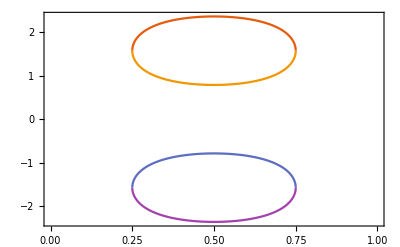

```mathematica
<<MaTeX`
Plot[Evaluate@(solutions/.{θ->x π}),{x,1/4,3/4}, GridLines->{{1/4,3/4},{}},PlotTheme->"Scientific",PlotRange->{{0,1},Full},FrameLabel->MaTeX[{"\\theta","\\phi"}]]
```

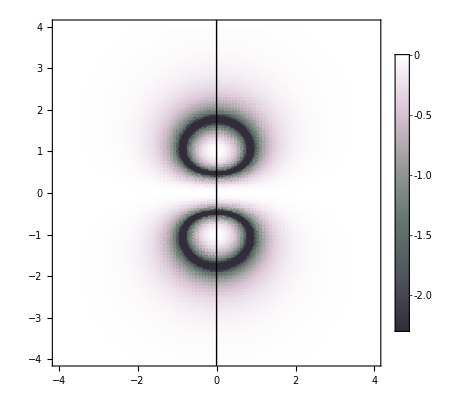

```mathematica
(* orthogonality between skyrmion and anti-skyrmion magnetization in real-space *)
clip=Log[10^-1];
overlap=DensityPlot[Log[Abs[4m[θsk[Norm[{x,y}]] ,Φ[ArcTan[x,y]]].m[θsk[Norm[{x,y}]] ,-Φ[ArcTan[x,y]]]]],{x,-L,L},{y,-L,L},PlotLegends->Automatic,PlotPoints->100,PlotTheme->"Scientific",ColorFunction->(ColorData["PigeonTones"][Rescale[#,{clip,0}]]&),ColorFunctionScaling->False,PlotRange->{clip,0},ClippingStyle->Black,GridLines->None,GridLinesStyle->{{Dashed,Black},{}},ClippingStyle->Red,FrameLabel->MaTeX[{"x","y"}],Exclusions->None];
Show[overlap,Graphics[Line[{-2L{Sin[ϕ0],Cos[ϕ0]},2L{Sin[ϕ0],Cos[ϕ0]}}]]]
```

```mathematica
Show[{skCart,askCart}]
```

-Graphics3D-

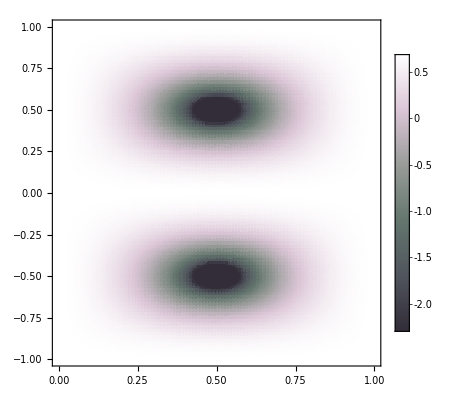

```mathematica
(* orthogonality between quantum skyrmion and quantum anti-skyrmion *)
$Assumptions=0<θ<=π&&-π<ϕ<=π;
clip=Log[10^-1];
qoverlap=DensityPlot[Log[4m[θ π,ϕ π].m[θ π,-ϕ π]+1],{θ,10^-12,1},{ϕ,-1+10^-12,1},PlotLegends->Automatic,PlotPoints->100,PlotTheme->"Scientific",ColorFunction->(ColorData["PigeonTones"][Rescale[#,{clip,Log[2]}]]&),ColorFunctionScaling->False,PlotRange->{clip,Log[2]},ClippingStyle->Black,PlotRange->Automatic, GridLines->{{1/4,1/2,3/4},{-0.5,0.5}},GridLinesStyle->{{Dashed,Black},{Dashed,Black}},FrameLabel->MaTeX[{"\\theta","\\phi"}]]
```

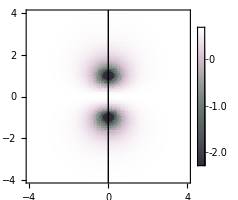

```mathematica
(* orthogonality between quantum skyrmion and anti-skyrmion wave function in real-space *)
clip=Log[10^-1];
overlap=DensityPlot[Log[4m[θsk[Norm[{x,y}]] ,Φ[ArcTan[x,y]]].m[θsk[Norm[{x,y}]] ,-Φ[ArcTan[x,y]]]+1],{x,-L,L},{y,-L,L},PlotLegends->Automatic,PlotPoints->100,PlotTheme->"Scientific",ColorFunction->(ColorData["PigeonTones"][Rescale[#,{clip,Log[2]}]]&),ColorFunctionScaling->False,PlotRange->{clip,Log[2]},ClippingStyle->Black,GridLines->None,GridLinesStyle->{{Dashed,Black},{}},ClippingStyle->Red,FrameLabel->MaTeX[{"x","y"}],Exclusions->None];
Show[overlap,Graphics[Line[{-2L{Sin[ϕ0],Cos[ϕ0]},2L{Sin[ϕ0],Cos[ϕ0]}}]],ImageSize->200]
```

```mathematica
dn={0,1};
S={sx,sy,sz} = Table[PauliMatrix[i]/2,{i,3}];
```

```mathematica
Clear[R]
R[θ_,ϕ_]:=MatrixExp[-ⅈ sz ϕ].MatrixExp[-ⅈ sy (θ-π)]
sk=R[θ,ϕ].dn;
ask=R[θ,-ϕ].dn;
Table[sk†.s.sk,{s,S}]-m[θ,ϕ]//FullSimplify
Table[ask†.s.ask,{s,S}]-m[θ,-ϕ]//FullSimplify
```

{0,0,0}

{0,0,0}

```mathematica
(* for each spin, the overlap is given by a product of the kind *)
ovl=sk†.ask//FullSimplify
```

Cos[ϕ]+ⅈ Cos[θ] Sin[ϕ]

```mathematica
$Assumptions=-π<ϕ<=π&&0<θ<π;
√(Re[ovl]^2+Im[ovl]^2)//FullSimplify
```

√(Cos[ϕ]^2+Cos[θ]^2 Sin[ϕ]^2)

```mathematica
ovl**ovl//FullSimplify
```

Cos[ϕ]^2+Cos[θ]^2 Sin[ϕ]^2

```mathematica
ovl**ovl-(2m[θ,ϕ].m[θ,-ϕ]+1/2)//TrigExpand//FullSimplify
```

0

```mathematica
4m[θ,ϕ].m[θ,-ϕ]+1//FullSimplify
```

1/2 (3+Cos[2 θ]+2 Cos[2 ϕ] Sin[θ]^2)

```mathematica
2m[θ,ϕ].m[θ,-ϕ]-(Re[ovl]^2+Im[ovl]^2)//FullSimplify
```

-1/2

```mathematica
2M[θ,ϕ,c]//FullSimplify
```

{Cos[ϕ] Sin[θ],(-1+2 c) Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
M[θ,ϕ,c].M[θ,ϕ,c]//ExpandAll//FullSimplify
```

1/4 (Cos[θ]^2+Sin[θ]^2 (Cos[ϕ]^2+(1-2 c)^2 Sin[ϕ]^2))

```mathematica
Grad[M[θ,ϕ,c].M[θ,ϕ,c],{θ,ϕ}]//FullSimplify
Solve[%=={0,0},{θ,ϕ}]
```

{(-1+c) c Sin[2 θ] Sin[ϕ]^2,(-1+c) c Sin[θ]^2 Sin[2 ϕ]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ϕ→ConditionalExpression[0, 0<θ<π]},{ϕ→ConditionalExpression[π, 0<θ<π]},{θ→π/2,ϕ→0},{θ→π/2,ϕ→-π/2},{θ→π/2,ϕ→π/2},{θ→π/2,ϕ→π}}

```mathematica
M[π/2,π/2,c].M[π/2,π/2,c]
```

(-1/2+c)^2

```mathematica
hatM[θ_,ϕ_,c_]=(2M[θ,ϕ,c])/(√(Cos[θ]^2+Sin[θ]^2 (Cos[ϕ]^2+(1-2 c)^2 Sin[ϕ]^2)))
```

{(Cos[ϕ] Sin[θ])/(√(Cos[θ]^2+Sin[θ]^2 (Cos[ϕ]^2+(1-2 c)^2 Sin[ϕ]^2))),(2 (-1/2 Sin[θ] Sin[ϕ]+c Sin[θ] Sin[ϕ]))/(√(Cos[θ]^2+Sin[θ]^2 (Cos[ϕ]^2+(1-2 c)^2 Sin[ϕ]^2))),Cos[θ]/(√(Cos[θ]^2+Sin[θ]^2 (Cos[ϕ]^2+(1-2 c)^2 Sin[ϕ]^2)))}

```mathematica
hatM[θ,ϕ,c].hatM[θ,ϕ,c]//FullSimplify
```

1

```mathematica
e1=hatM[θ[x,y],ϕ[x,y],c].Cross[D[hatM[θ[x,y],ϕ[x,y],c],x],D[hatM[θ[x,y],ϕ[x,y],c],y]]//FullSimplify
```

((-1+2 c) Sin[θ[x,y]] (ϕ^(0,1)[x,y] θ^(1,0)[x,y]-θ^(0,1)[x,y] ϕ^(1,0)[x,y]))/((1+(-1+c) c-(-1+c) c (Cos[2 θ[x,y]]+2 Cos[2 ϕ[x,y]] Sin[θ[x,y]]^2))^(3/2))

```mathematica
e2=M[θ[x,y],ϕ[x,y],c].Cross[D[M[θ[x,y],ϕ[x,y],c],x],D[M[θ[x,y],ϕ[x,y],c],y]]/(√(M[θ[x,y],ϕ[x,y],c].M[θ[x,y],ϕ[x,y],c]))^3//ExpandAll//TrigExpand//FullSimplify
```

((-1+2 c) Sin[θ[x,y]] (ϕ^(0,1)[x,y] θ^(1,0)[x,y]-θ^(0,1)[x,y] ϕ^(1,0)[x,y]))/((1+(-1+c) c-(-1+c) c (Cos[2 θ[x,y]]+2 Cos[2 ϕ[x,y]] Sin[θ[x,y]]^2))^(3/2))

```mathematica
e1-e2
```

0

```mathematica
$Assumptions=s>0&&0<θ<=π&&-π<ϕ<=π;
rv[θ_,ϕ_]=2 s m[θ,ϕ]
```

{s Cos[ϕ] Sin[θ],s Sin[θ] Sin[ϕ],s Cos[θ]}

```mathematica
(* this one is normalized *)
θv[θ_,ϕ_]=D[rv[θ,ϕ],θ]/s
θv[t,p].θv[t,p]//FullSimplify
```

{Cos[θ] Cos[ϕ],Cos[θ] Sin[ϕ],-Sin[θ]}

1

```mathematica
Clear[ϕvtp,ϕv]
ϕvtp[θ_,ϕ_]=D[rv[θ,ϕ],ϕ]
hϕ[t_,p_]=√(ϕvtp[t,p].ϕvtp[t,p])//FullSimplify
ϕv[θ_,ϕ_]=ϕvtp[θ,ϕ]/hϕ[θ,ϕ]//FullSimplify
```

{-s Sin[θ] Sin[ϕ],s Cos[ϕ] Sin[θ],0}

s √(Sin[t]^2)

{-Sin[ϕ],Cos[ϕ],0}

```mathematica
D[ToSphericalCoordinates[{x,y,z}][[2]],x]//FullSimplify
```

(x z)/(√(x^2+y^2) (x^2+y^2+z^2))

```mathematica
{rv[θ,ϕ]/s,θv[θ,ϕ],ϕv[θ,ϕ]}ᵀ.{rv[θ,ϕ]/s,θv[θ,ϕ],ϕv[θ,ϕ]}//FullSimplify
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Inverse[{rv[θ,ϕ]/s,θv[θ,ϕ],ϕv[θ,ϕ]}]//FullSimplify
```

{{Cos[ϕ] Sin[θ],Cos[θ] Cos[ϕ],-Sin[ϕ]},{Sin[θ] Sin[ϕ],Cos[θ] Sin[ϕ],Cos[ϕ]},{Cos[θ],-Sin[θ],0}}

```mathematica
D[ArcTan[x,y],y]
```

x/(x^2+y^2)

```mathematica
D[hatM[θ[x,y],ϕ[x,y],c],x].D[hatM[θ[x,y],ϕ[x,y],c],y]//FullSimplify
```

(8 θ^(0,1)[x,y] ((1+2 (-1+c) c-2 (-1+c) c Cos[2 ϕ[x,y]]) θ^(1,0)[x,y]+(-1+c) c Sin[2 θ[x,y]] Sin[2 ϕ[x,y]] ϕ^(1,0)[x,y])+4 ϕ^(0,1)[x,y] (2 Sin[θ[x,y]]^2 ϕ^(1,0)[x,y]+(-1+c) c (2 Sin[2 θ[x,y]] Sin[2 ϕ[x,y]] θ^(1,0)[x,y]+(-2 (-3+Cos[2 θ[x,y]]) Sin[θ[x,y]]^2+Cos[2 ϕ[x,y]] Sin[2 θ[x,y]]^2) ϕ^(1,0)[x,y])))/(2 (2+2 (-1+c) c-2 (-1+c) c (Cos[2 θ[x,y]]+2 Cos[2 ϕ[x,y]] Sin[θ[x,y]]^2))^2)